```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
hwBearingWeights={
{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}},{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}},{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}},{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}},{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}},{{0.866025,-0.500000},{0.000000,-1.000000},{-0.866025,-0.500000},{-0.866025,0.500000},{0.000000,1.000000},{0.866025,0.500000}}
};
hwHeadingWeights={
{{-1.000000,0.000000},{-0.500000,0.866025},{0.500000,0.866025},{1.000000,0.000000},{0.500000,-0.866025},{-0.500000,-0.866025}},
{{-0.500000,-0.866025},{-1.000000,0.000000},{-0.500000,0.866025},{0.500000,0.866025},{1.000000,0.000000},{0.500000,-0.866025}},{{0.500000,-0.866025},{-0.500000,-0.866025},{-1.000000,0.000000},{-0.500000,0.866025},{0.500000,0.866025},{1.000000,0.000000}},{{1.000000,0.000000},{0.500000,-0.866025},{-0.500000,-0.866025},{-1.000000,0.000000},{-0.500000,0.866025},{0.500000,0.866025}},{{0.500000,0.866025},{1.000000,0.000000},{0.500000,-0.866025},{-0.500000,-0.866025},{-1.000000,0.000000},{-0.500000,0.866025}},{{-0.500000,0.866025},{0.500000,0.866025},{1.000000,0.000000},{0.500000,-0.866025},{-0.500000,-0.866025},{-1.000000,0.000000}}
};
```

```mathematica
N@(390804/10000)
```

39.0804

```mathematica
Table[Mod[j+(6-i),6]+1,{i,0,5},{j,0,5}]
```

{{1,2,3,4,5,6},{6,1,2,3,4,5},{5,6,1,2,3,4},{4,5,6,1,2,3},{3,4,5,6,1,2},{2,3,4,5,6,1}}

```mathematica
Partition[sampleMeas,6]
```

{{-10,-11,2,11,11,54},{9,10,8,101,450,68},{-9,-4,40,371,304,67},{13,5,21,28,5,57},{-10,14,27,-1,10,61},{-15,-18,-33,4,22,49}}

```mathematica
dropletSensorRadius=2.5;
```

```mathematica
{Cos[#],Sin[#]}&/@basisAngle
```

{{(√3)/2,-1/2},{0,-1},{-(√3)/2,-1/2},{-(√3)/2,1/2},{0,1},{(√3)/2,1/2}}

```mathematica
headingBasisAngle={π,-(2π)/3,-π/3,0,π/3,2 π/3};
```

```mathematica
TableForm@Table[ArcTan@@bearingWeightsMat⟦i,j⟧,{i,1,6},{j,1,6}]
```

-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6

```mathematica
TableForm@Table[basisAngle,6]
```

-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6
-π/6 | -π/2 | -(5 π)/6 | (5 π)/6 | π/2 | π/6

```mathematica
headingBasis={{-1,0},{-1/2,(√3)/2},{1/2,(√3)/2},{1,0},{1/2,-(√3)/2},{-1/2,-(√3)/2}};
headingWeightsMat=(Table[headingBasis⟦Mod[j+(6-i),6]+1⟧,{i,0,5},{j,0,5}]);
(*headingWeightsMat=(Table[{Cos[#],Sin[#]}&@headingBasisAngle⟦Mod[j+(6-i),6]+1⟧,{i,0,5},{j,0,5}]);*)
bearingBasis={{(√3)/2,-1/2},{0,-1},{-(√3)/2,-1/2},{-(√3)/2,1/2},{0,1},{(√3)/2,1/2}};
bearingWeightsMat=Table[bearingBasis,6];
sensorModel[α_]:=With[{a=Abs[α]},
If[a≥1.5,0,
If[a≤0.62,
1-a^4,
0.125/a^4
]
]
];
emitterModel[β_]:=With[{b=Abs[β]},
If[b≥1.5,0,
If[b≤0.72,
0.94+0.5*b^2-b^4,
0.25/b^4
]
]
];
inverseAmplitudeModel[l_]:=If[l≥2597.1,0.5,√(13427.5/(l-3.90804)-5.17716)+0.528561];
basisAngle={-π/6,-π/2,-(5π)/6,(5π)/6,π/2,π/6};
GetBearing[meas_]:=With[{bm=Partition[meas,6]},
N[Mod[ArcTan@@Total[(bm*hwBearingWeights),2],2π,-π]]
];
GetHeading[meas_]:=With[{bm=Partition[meas,6]},
N[Mod[ArcTan@@Total[(bm*hwHeadingWeights),2],2π,-π]]
];
dropletSensorRadius=2.5;
```

```mathematica
Clear[dropletRadius]
```

```mathematica
InitialRangeGuess[b_,h_,meas_]:=Module[{bm=Partition[meas,6],bestS,bestE,α,β,expCon,amplitude,rMagEst,Rx,Ry},
bestS=Mod[6-Ceiling[(3*b)/π],6]+1;
α=Mod[b-basisAngle⟦bestS⟧,2π,-π];
bestE=Mod[6-Ceiling[(3*(b-h-π))/π],6]+1;
β=Mod[b-h-basisAngle⟦bestE⟧-π,2π,-π];
If[-π/2<α<π/2∧-π/2<β<π/2,
expCon=sensorModel[α]*emitterModel[β];
If[expCon>0,
amplitude=(bm⟦bestE⟧⟦bestS⟧)/expCon;
rMagEst=inverseAmplitudeModel[amplitude];
Rx=rMagEst*Cos[b]+dropletSensorRadius*(bearingBasis⟦bestS,1⟧-headingBasis⟦bestE,1⟧);
Ry=rMagEst*Sin[b]+dropletSensorRadius*(bearingBasis⟦bestS,2⟧-headingBasis⟦bestE,2⟧);
√(Rx^2+Ry^2)
,0]
,0]
];
RangeEstimate[iR_,b_,h_,meas_]:=Module[{bm=Partition[meas,6],rangeMat,maxE,maxS,maxBright=0,rangeSubmat,bmSubmat,weights},
rangeMat=Table[
If[bm⟦e,s⟧>0,
If[bm⟦e,s⟧>maxBright,
maxBright=bm⟦e,s⟧;
maxE=e;
maxS=s;
];
Module[{sRX,sTX,α,β,expCon,calcMag,calcR},
sRX=RotationMatrix[basisAngle⟦s⟧].{0,dropletSensorRadius};
sTX=RotationMatrix[basisAngle⟦e⟧+h].{0,dropletSensorRadius};
sTX=sTX+RotationMatrix[b].{0,iR};
(*sRXx=dropletRadius*bearingBasis⟦s,1⟧;
sRXy=dropletRadius*bearingBasis⟦s,2⟧;
sTXx=dropletRadius*Cos[basisAngle⟦e⟧+h]+iR*Cos[b];
sTXy=dropletRadius*Sin[basisAngle⟦e⟧+h]+iR*Sin[b];*)
α=Mod[ArcTan@@(sTX-sRX)-basisAngle⟦s⟧+π/2,2π,-π];
β=Mod[ArcTan@@(sRX-sTX)-basisAngle⟦e⟧-h+π/2,2π,-π];
(*α=Mod[ArcTan[sTXx-sRXx,sTXy-sRXy]-basisAngle⟦s⟧,2π,-π];
β=Mod[ArcTan[sRXx-sTXx,sRXy-sTXy]-basisAngle⟦e⟧-h,2π,-π];*)
expCon=sensorModel[α]*emitterModel[β];
calcMag=If[expCon>0,
inverseAmplitudeModel[bm⟦e,s⟧/expCon],
0];
calcR={0,calcMag}.RotationMatrix[α]+sRX+sTX;
(*calcRx=calcMag*Cos[α]+sRXx-dropletRadius*Cos[basisAngle⟦e⟧+h];
calcRy=calcMag*Sin[α]+sRXy-dropletRadius*Sin[basisAngle⟦e⟧+h];
√(calcRx^2+calcRy^2)*)
Norm[calcR];
Mod[#,360,-180]&/@{α,β}/°
],
0],
{e,1,6},{s,1,6}];
rangeSubmat=Partition[rangeMat,{3,3},{1,1},{{2,2},{2,2}}]⟦maxE,maxS⟧;
bmSubmat=Partition[bm,{3,3},{1,1},{{2,2},{2,2}}]⟦maxE,maxS⟧;
weights=bmSubmat/Norm[bmSubmat,"Frobenius"];
Total[weights*rangeSubmat,2];
rangeMat
]
GetResults[meas_]:=
Module[{b=Mod[GetBearing[meas]+π/2,2π,-π],h=Mod[GetHeading[meas]+π/2,2π,-π],iR,R},
iR=InitialRangeGuess[b,h,meas];
R=RangeEstimate[iR,b,h,meas];
{Round[10*R],Mod[Round[(b/°)],360,-180],Mod[Round[h/°],360,-180]}
];
TableForm@{{"","R","B","H"},Prepend[GetResults[sampleMeas],"Calc"],Prepend[trueVals,"True"]}
```

| R | B | H
Calc | 600
1402 | 0 | -1789
1413 | -1177
1425 | -578
1424 | 0
613
-1585 | 0 | -1775
-1573 | -1164
-1562 | -565
-1563 | 24
-1575
621
-978 | 1221
-977 | -1767
-966 | -1157
-955 | -557
-956 | 0
0 | 1216
-382 | 0 | -1162
-360 | -563
-361 | 26
-372
0 | 0 | 0 | -1174
227 | -575
227 | 14
216
596
797 | 1196
797 | -1793
809 | -1182
820 | -583
819 | 0 | -148 | 100
True | 137 | -141 | 123

```mathematica
With[{meas=sampleMeas},Module[{b=Mod[GetBearing[meas]+π/2,2π,-π],h=Mod[GetHeading[meas]+π/2,2π,-π],iR,R},
iR=InitialRangeGuess[b,h,meas];
R=RangeEstimate[iR,b,h,meas];
{trueVals,MatrixForm[R],MatrixForm[Partition[meas⟦;;36⟧,6]]}
]]
```

{{137,-141,123},({59.9953,140.179} | 0 | {-178.852,141.331} | {-117.727,142.457} | {-57.7776,142.406} | 0
{61.2676,-158.549} | 0 | {-177.532,-157.349} | {-116.419,-156.236} | {-56.4998,-156.316} | {2.35827,-157.458}
{62.0582,-97.7585} | {122.105,-97.7119} | {-176.737,-96.5532} | {-115.654,-95.4708} | {-55.75,-95.5667} | 0
0 | {121.623,-38.1938} | 0 | {-116.181,-35.9973} | {-56.2633,-36.08} | {2.63458,-37.1821}
0 | 0 | 0 | {-117.439,22.7444} | {-57.4942,22.6891} | {1.41874,21.602}
{59.5607,79.744} | {119.551,79.7341} | {-179.326,80.8573} | {-118.218,81.9649} | {-58.2576,81.9257} | 0),(4 | -2 | 2 | 87 | 235 | -8
5 | -22 | 5 | 310 | 197 | 8
5 | 22 | 3 | 44 | 5 | -12
-4 | 20 | -2 | 35 | 24 | 17
-7 | -8 | -7 | 7 | 18 | 1
2 | 19 | 11 | 25 | 11 | -1)}

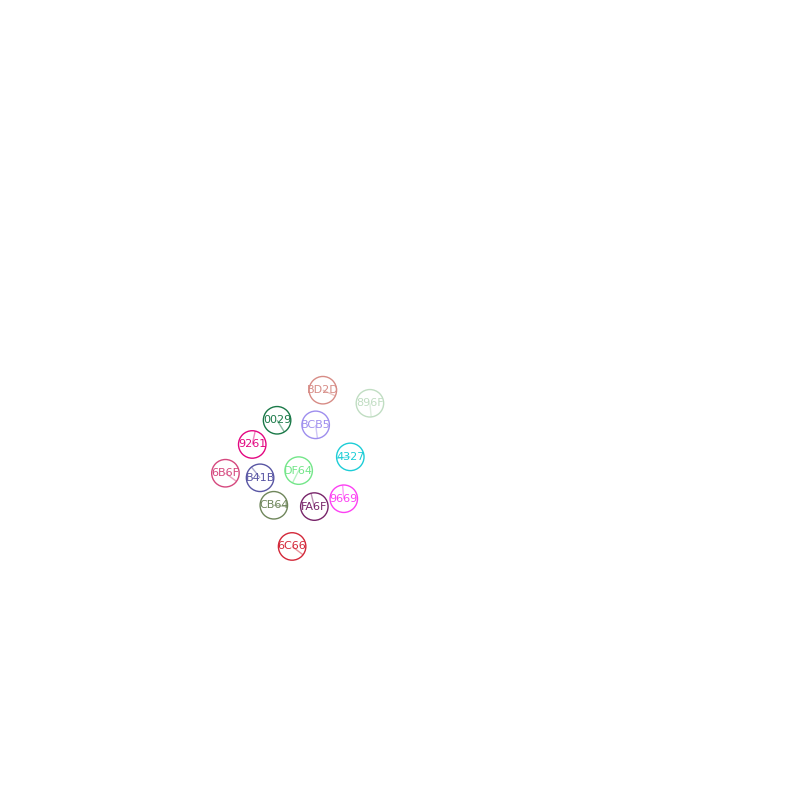

```mathematica
Length@row
```

39

```mathematica
MatrixForm[Partition[sampleMeas,6]]
```

(4 | -2 | 2 | 87 | 235 | -8
5 | -22 | 5 | 310 | 197 | 8
5 | 22 | 3 | 44 | 5 | -12
-4 | 20 | -2 | 35 | 24 | 17
-7 | -8 | -7 | 7 | 18 | 1
2 | 19 | 11 | 25 | 11 | -1)

```mathematica
row={4,-2,2,87,235,-8,5,-22,5,310,197,8,5,22,3,44,5,-12,-4,20,-2,35,24,17,-7,-8,-7,7,18,1,2,19,11,25,11,-1,137,-141,123};
sampleMeas=row⟦;;36⟧;
trueVals=row⟦37;;39⟧;
```

```mathematica
trueVals
```

{111,-170,-109}

```mathematica
dat=Import["results.csv",HeaderLines->1];
```

```mathematica
results=Parallelize[GetResults[#⟦;;36⟧]&/@dat];
```

```mathematica
comparison=(Abs/@(GetResults[#⟦;;36⟧]-#⟦37;;39⟧))&/@dat;
```

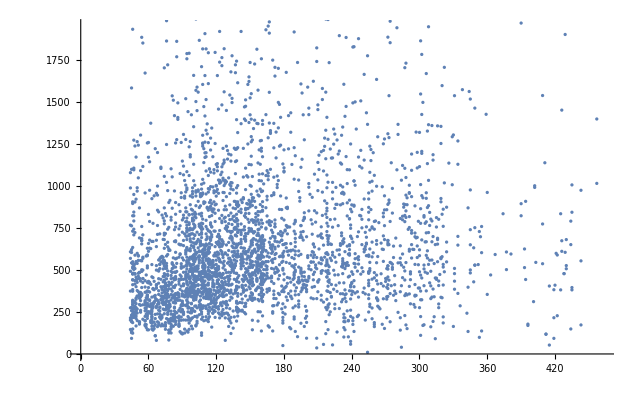

```mathematica
ListPlot[{dat⟦;;,37⟧,(results⟦;;,1⟧)}ᵀ]
```

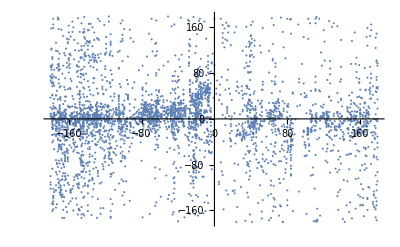

```mathematica
ListPlot[{Mod[#,360,-180]&/@dat⟦;;,38⟧,Mod[#,360,-180]&/@(dat⟦;;,38⟧-results⟦;;,2⟧)}ᵀ]
```

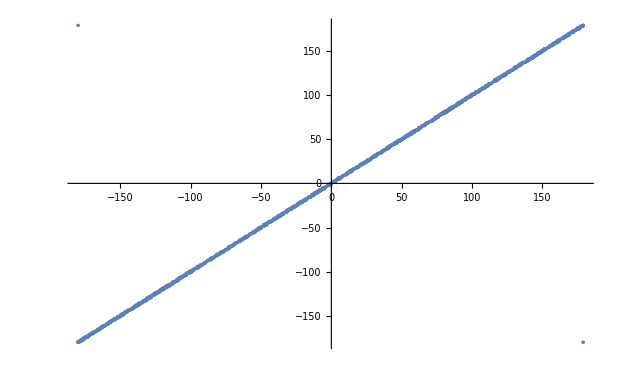

```mathematica
ListPlot[{(Mod[#,360,-180]&/@(dat⟦;;,40⟧-dat⟦;;,41⟧)),(Mod[#,360,-180]&/@dat⟦;;,39⟧)}ᵀ]
```

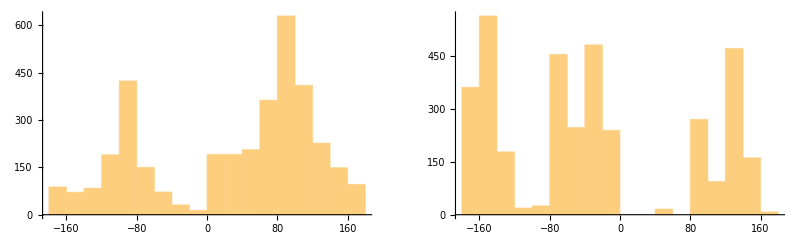

```mathematica
GraphicsRow[{Histogram@(Mod[#,360,-180]&/@comparison⟦;;,2⟧),Histogram@(Mod[#,360,-180]&/@dat⟦;;,41⟧)},ImageSize->800]
```

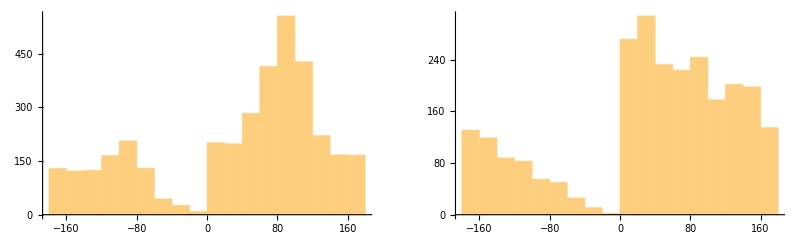

```mathematica
GraphicsRow[{Histogram@(Mod[#,360,-180]&/@comparison⟦;;,3⟧),Histogram@(Mod[#,360,-180]&/@comparisonFlipped⟦;;,3⟧)},ImageSize->800]
```